# Osculating Orbital Elements

The method of osculating geodesics follows an orbit under a force as a sequence of geodesics: at each moment the orbit is the geodesic with the same position and velocity, and the force changes which geodesic that is. This package integrates those equations for bound orbits in Kerr spacetime, and also drives inspirals with fluxes, orbit-averaged rates of change of the elements. It builds on KerrGeodesics.

```mathematica
Needs["OsculatingOrbitalElements`"]
```

### An inspiral

OsculatingInspiral takes an Association of parameters: the spin a, the small mass ratio ϵ, the initial semi-latus rectum p, eccentricity e and inclination x = cos ι, and a force, a flux or both. Here gas drag drives the inspiral until it reaches the separatrix:

```mathematica
inspiral=OsculatingInspiral[Association["a"->0.9,"ϵ"->1/10^3,"p"->8,"e"->0.3,"x"->0.6,"Force"->ForceModel["GasDrag","Coefficient"->1/10^4]]]
```

OsculatingInspiralFunction[…]

The result is an OsculatingInspiralFunction. It gives the position {t, r, θ, ϕ} at a time, and its properties are functions of the time:

```mathematica
inspiral[100]
```

{100,10.9391,2.09711,4.57264}

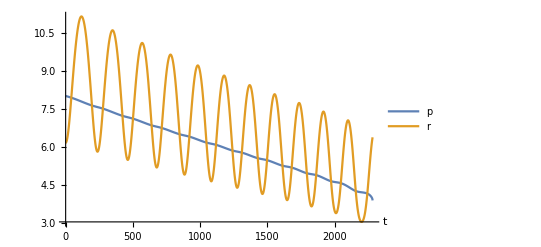

```mathematica
Plot[{inspiral["p"][t],inspiral["r"][t]},{t,0,inspiral["Domain"]⟦2⟧},PlotLegends->{"p","r"},AxesLabel->{"t",None}]
```

"StopReason" says why the integration stopped. By default it stops when p comes within ϵ of the separatrix:

```mathematica
inspiral["StopReason"]
```

SeparatrixBuffer

### Forces

A force is a ForceModel. The built-in models are "GasDrag", which needs a "Coefficient", "EMConservative" and "FastGSF", a fit to the first-order self-force in Schwarzschild. A custom force is a function of the elements, the phases, the azimuth and the coordinate time, (a, p, e, x, ψr, ψθ, ϕ, t), that returns the covariant components {F_r, F_θ, F_ϕ}; F_t follows from orthogonality to the velocity. This one is a torque, which reduces the angular momentum, and so x:

```mathematica
torque=ForceModel[Function[{a,p,e,x,ψr,ψθ,ϕ,t},{0,0,-1}],"Name"->"Torque"];
```

```mathematica
tilted=OsculatingInspiral[Association["a"->0.5,"ϵ"->1/10^4,"p"->10,"e"->0.2,"x"->0.8,"Force"->torque],IntegrationLimit->3000];
```

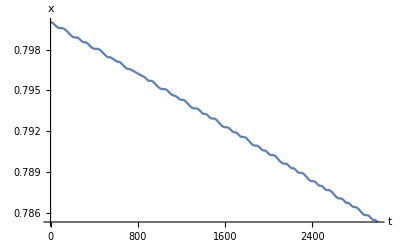

```mathematica
Plot[tilted["x"][t],{t,0,3000},AxesLabel->{"t","x"}]
```

A force is multiplied by the mass ratio ϵ unless it says otherwise; gas drag does not scale with ϵ, since its strength is its coefficient. Several forces add:

```mathematica
both=OsculatingInspiral[Association["a"->0,"ϵ"->1/10^3,"p"->10,"e"->0.1,"x"->1,"Force"->{"FastGSF",ForceModel["GasDrag","Coefficient"->1/10^4]}]];
```

```mathematica
{both["Domain"],both["StopReason"]}
```

{{0,1014.07},SeparatrixBuffer}

### Fluxes

A flux is a FluxModel: orbit-averaged rates of change of p, e and x, or of the energy, angular momentum and Carter constant, with respect to coordinate time. It changes only the slowly varying elements, and the phases keep their geodesic rates. "Peters" is the leading-order gravitational-wave flux:

```mathematica
peters=OsculatingInspiral[Association["a"->0.9,"ϵ"->1/10^2,"p"->12,"e"->0.3,"x"->0.7,"Flux"->"Peters"]];
```

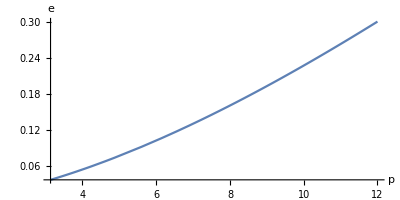

```mathematica
ParametricPlot[{peters["p"][t],peters["e"][t]},{t,0,peters["Domain"]⟦2⟧},AxesLabel->{"p","e"},AspectRatio->1/2]
```

The orbit average of a force is a flux. Driven by the force and by its averaged flux, an inspiral changes in the same way, apart from oscillations of size ϵ:

```mathematica
drag=ForceModel["GasDrag","Coefficient"->1/10^4];
```

```mathematica
{forced,fluxed}=(OsculatingInspiral[Association["a"->0.5,"ϵ"->1/10^4,"p"->10,"e"->0.2,"x"->1,#1],IntegrationLimit->1000]&)/@{"Force"->drag,"Flux"->FluxModel[drag]};
```

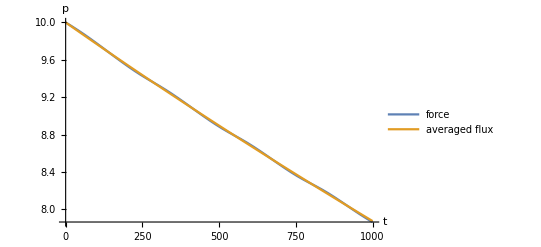

```mathematica
Plot[{forced["p"][t],fluxed["p"][t]},{t,0,1000},PlotLegends->{"force","averaged flux"},AxesLabel->{"t","p"}]
```

Forces and fluxes can drive an inspiral together, for example a gravitational-wave flux and gas drag.

### Special orbits

The radial equations are regular for circular orbits, and the equation for x is regular at x = 0, so an inspiral can pass from prograde to retrograde. Orbits that start exactly polar, x = 0, are not supported. Schwarzschild is a = 0.

Equatorial orbits, x = ±1, are a special case: x stays ±1 and θ = π/2, so the force must have no θ component in the plane, and a flux must not change x. An orbit that starts circular stays circular under a flux. The Darwin phase is undefined on a circular orbit, and the Hughes phase on an equatorial one:

```mathematica
circular=OsculatingInspiral[Association["a"->0,"ϵ"->1/10^2,"p"->12,"e"->0,"x"->1,"Flux"->"Peters"],IntegrationLimit->1000];
```

```mathematica
{circular["e"][1000],circular["x"][1000],circular["ψr"][1000],circular["ψθ"][1000]}
```

{0.,1.,Missing[UndefinedAtZeroEccentricity],Missing[UndefinedForEquatorialOrbit]}

### Frequencies and angles

The inspiral also gives the Boyer-Lindquist frequencies of the osculating geodesic, Ωr, Ωθ and Ωϕ, from KerrGeodesics, and its Boyer-Lindquist action angles Φr, Φθ and Φϕ (Lynch and Burke 2025). Along a geodesic each angle advances at its frequency. Over an inspiral the angles accumulate, and differ from the integral of the frequencies by the force's effect on them, which is small until the orbit nears the separatrix. Here at t = 2000, before the plunge:

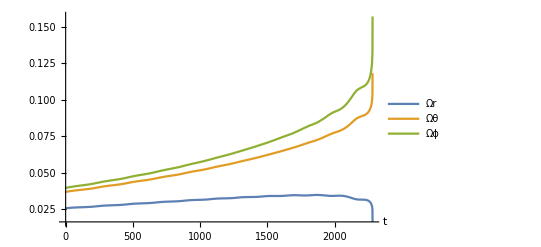

```mathematica
Plot[Evaluate[(inspiral[#1][t]&)/@{"Ωr","Ωθ","Ωϕ"}],{t,0,inspiral["Domain"]⟦2⟧},PlotLegends->{"Ωr","Ωθ","Ωϕ"},AxesLabel->{"t",None}]
```

```mathematica
Table[{inspiral["Φ"<>k][2000]-inspiral["Φ"<>k][0],NIntegrate[inspiral["Ω"<>k][t],{t,0,2000}]},{k,{"r","θ","ϕ"}}]
```

{{62.4876,62.5026},{107.,106.968},{119.89,119.836}}

### Options

IntegrationLimit, SeparatrixBuffer and pMin control where the integration stops, Parametrisation -> "Mino" integrates in Mino time, and any option of NDSolve is passed to NDSolve.

### The earlier functions

The earlier functions of the package, such as GenericKerrpexBL and SchwarzOsculatingOrbitalElements, keep working but are legacy; OsculatingInspiral, ForceModel and FluxModel supersede them.

Related Guides

Osculating Orbital Elements

## Metadata

### Categorization

Tech Note

OsculatingOrbitalElements

OsculatingOrbitalElements`

OsculatingOrbitalElements/tutorial/OsculatingOrbitalElements

### Keywords

osculating orbital elements

inspiral

Kerr